## Formulae an

```mathematica
MpgChain[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain[contract],{e,ChromaticPolynomial[g,4]/24}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
MpgChain3[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain3[contract],ChromaticPolynomial[g,4]/24];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
Monitor[Select[Table[k->With[{l=Differences[Reverse[MpgChain3[ReadGrof[k]]]]},{Min[l],Max[l]}],{k,10}],#[[2]]≠{0,0}&],k]
```

{4→{0,3},6→{0,3},7→{0,3}}

```mathematica
cm=72/2.54;
```

```mathematica
Clear[MpgChain2]
```

```mathematica
MpgChain2[g_,previous_:{}, positions_:Null,size_:{}]:=Block[{contract, result, coord, newPos=positions,newSize=size, layout},
If[VertexCount[g]==3,Return[
coord=Table[newPos[[k]],{k,VertexList[g]}];
{Labeled[
Graph[
g,
ImageSize->newSize,
VertexLabelStyle->Directive[Darker[Green],Italic,20],
VertexLabels->Map[If[MemberQ[previous,#],#->ToString[previous],#->#]&,VertexList[g]],
GraphHighlightStyle->"Thick",
GraphHighlight->CollectMPGEdges[g], 
VertexStyle->Map[#->Yellow&,previous], 
VertexSize->Map[#->Large&,previous],
VertexCoordinates->coord
],{ChromaticPolynomial[g,4]/24,Map[VertexDegree[g,#]&,Map[Column[{#,VertexDegree[g,#]}]&,Sort[VertexList[g]]]]}]}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
If[positions==Null,
layout = Graph[
SortGraph[g],
GraphLayout->"PlanarEmbedding",
GraphHighlightStyle->"Thick",
ImageSize->{12 cm,12 cm}, 
VertexCoordinates->Automatic
];
newPos=First[AbsoluteOptions[layout, VertexCoordinates]][[2]];
newSize=First[AbsoluteOptions[layout, ImageSize]][[2]];
Print[newSize]
];
coord=Table[newPos[[k]],{k,VertexList[g]}];
result=Prepend[MpgChain2[contract,{e[[1]],e[[2]]}, newPos,newSize],{e,Labeled[
Graph[
g,
GraphHighlightStyle->"Thick",
VertexLabels->Map[If[MemberQ[previous,#],#->ToString[previous],#->#]&,VertexList[g]],
GraphHighlight->Select[CollectMPGEdges[g],#=!=e&],
VertexLabelStyle->Directive[Darker[Green],Italic,20],
GraphLayout->{"EdgeLayout"->"HierarchicalEdgeBundling"},
ImageSize->newSize, 
AspectRatio->1,
EdgeStyle->{e->{Thick,Blue,Dashed}}, 
VertexStyle->Map[#->Yellow&,previous], 
VertexSize->Map[#->Large&,previous],
VertexCoordinates->coord
],{Column[ExplainContractionCounts[g,e]],Style[ChromaticPolynomial[g,4]/24,Green ],Map[Column[{#,VertexDegree[g,#]}]&,Sort[VertexList[g]]]}]}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

## experiments come

{340.157,340.157}

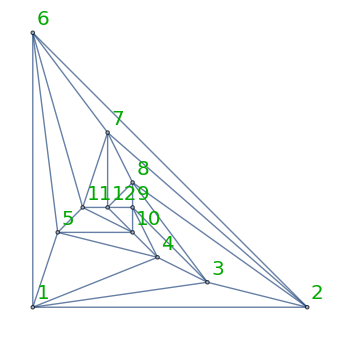
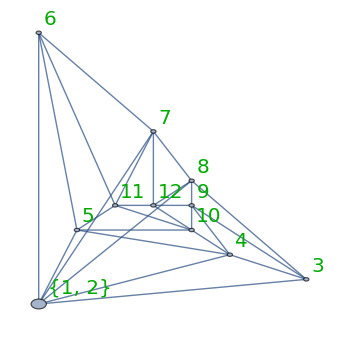
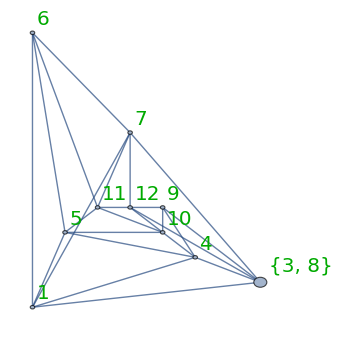
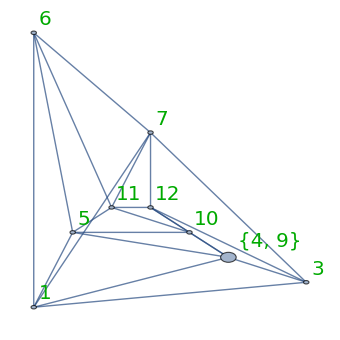
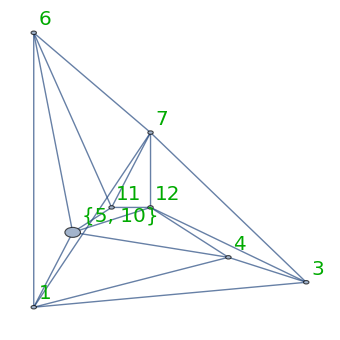
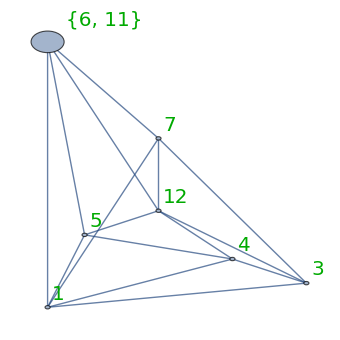
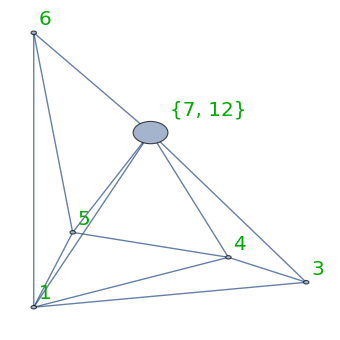
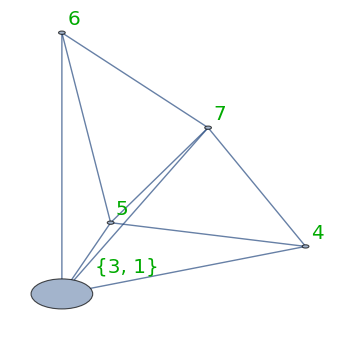
{{1<->2,-Graphics-{4
24,10,{1
5,2
5,3
5,4
5,5
5,6
5,7
5,8
5,9
5,10
5,11
5,12
5}}},{3<->8,-Graphics-{4
17,8,{1
6,3
4,4
5,5
5,6
4,7
5,8
5,9
5,10
5,11
5,12
5}}},{4<->9,-Graphics-{3
12,8,{1
5,3
5,4
5,5
5,6
4,7
5,9
4,10
5,11
5,12
5}}},{5<->10,-Graphics-{2
8,2,{1
5,3
4,4
5,5
5,6
4,7
5,10
4,11
5,12
5}}},{6<->11,-Graphics-{2
4,3,{1
5,3
4,4
4,5
5,6
4,7
5,11
4,12
5}}},{7<->12,-Graphics-{0
3,5,{1
5,3
4,4
4,5
4,6
4,7
4,12
5}}},{3<->1,-Graphics-{0
1,1,{1
5,3
3,4
4,5
4,6
3,7
5}}},{5<->4,-Graphics-{0
0,1,{1
4,4
3,5
4,6
3,7
4}}},{7<->6,-Graphics-{0
0,1,{1
3,4
3,6
3,7
3}}},-Graphics-{1,{VertexDegree[-Graphics-,1
2],VertexDegree[-Graphics-,4
2],VertexDegree[-Graphics-,6
2]}}}

```mathematica
MpgChain2[Graph[plantri [[1]] ] ]
```

{340.157,340.157}

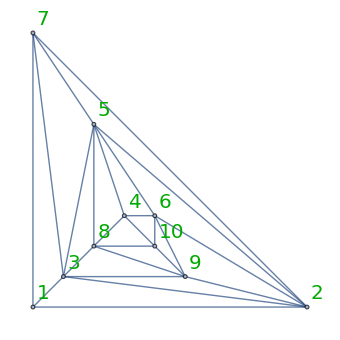
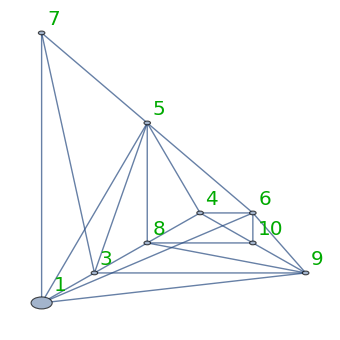
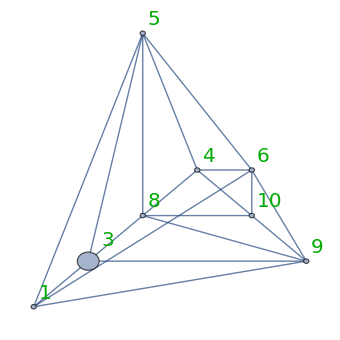
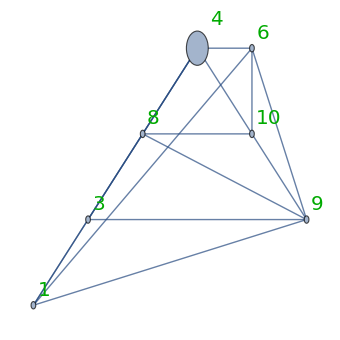
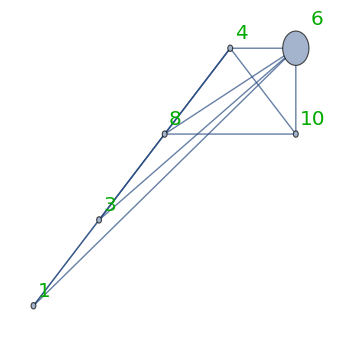
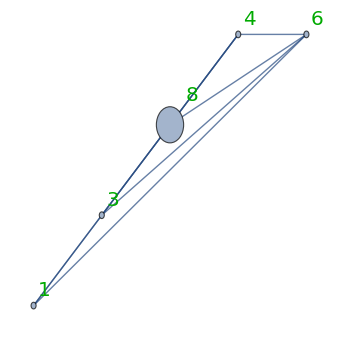
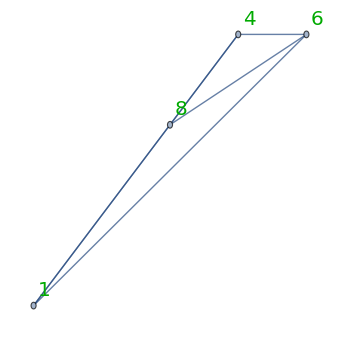
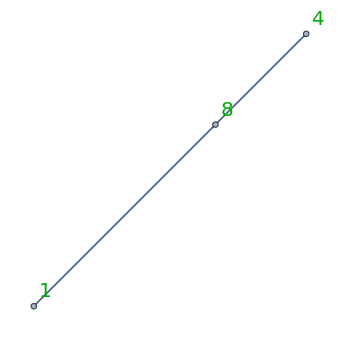
{{1<->2,-Graphics-{3
12,3,{3,6,6,4,6,5,5,5,4,4}}},{3<->7,-Graphics-{3
7,3,{5,3,6,5,5,5,4,4,5}}},{4<->5,-Graphics-{1
5,3,{5,5,5,5,4,4,4,4}}},{6<->9,-Graphics-{0
3,5,{4,5,4,4,4,4,5}}},{8<->10,-Graphics-{1
0,1,{4,3,3,4,5,5}}},{3<->1,-Graphics-{0
0,1,{3,4,4,4,3}}},{6<->4,-Graphics-{0
0,1,{3,3,3,3}}},-Graphics-{1,{2,2,2}}}

```mathematica
MpgChain2[ReadGrof[99] ]
```